MAT120           Assignment 5
 5. a)

```mathematica
DSolve[y'[x]==ⅇ^(3x+2y[x]),y[x],x]
```

{{y[x]→-1/2 Log[2 (-ⅇ^(3 x)/3-C[1])]}}

```mathematica
sol=y[x]/.%1/.C[1]->a
```

{-1/2 Log[2 (-a-ⅇ^(3 x)/3)]}

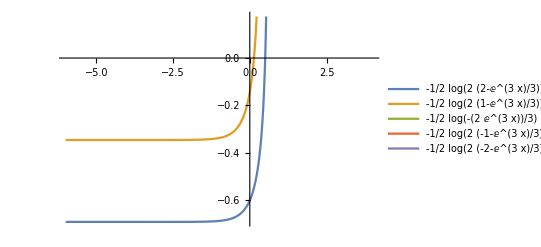

```mathematica
Plot[Evaluate[Table[sol,{a,-2,2 }]],{x,-6,4},PlotLegends->"Expressions"]
```

5. b)

```mathematica
DSolve[{y''[t]+2y'[t]+5y[t]==4 ⅇ^-t Cos[2t],y[1]==0,y'[0]==1},y[t],t]
```

{{y[t]→-1/(4 (2 Cos[2]+Sin[2]))ⅇ^-t (2 Cos[2] Cos[4] Cos[2 t]-2 Cos[2] Cos[2 t] Cos[4 t]+13 Cos[2 t] Sin[2]-Cos[2 t] Cos[4 t] Sin[2]+2 Cos[2 t] Sin[2] Sin[4]-5 Cos[2] Sin[2 t]-8 t Cos[2] Sin[2 t]+Cos[2] Cos[4] Sin[2 t]+4 Sin[2] Sin[2 t]-4 t Sin[2] Sin[2 t]+Sin[2] Sin[4] Sin[2 t]-2 Cos[2] Sin[2 t] Sin[4 t]-Sin[2] Sin[2 t] Sin[4 t])}}

```mathematica
y[t]/.%1/.t-> 4//N
```

{-0.145018}

5. c)

```mathematica
NDSolve[{x'[t]==x[t]-x[t]^2,x[0]==1/2},x[t],{t,0,5}]
```

{{x[t]→InterpolatingFunction[…][t]}}

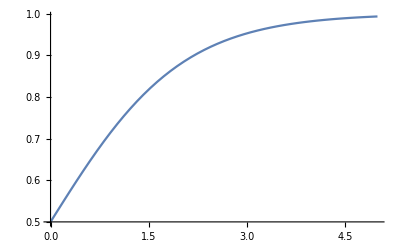

```mathematica
Plot[x[t]/.%3,{t,0,5},PlotRange->Full]
```